## Survival plots

What this plotting code generates : 
List Step Plots that show the survival of a event over time 
Input file : Excel sheet with data ...

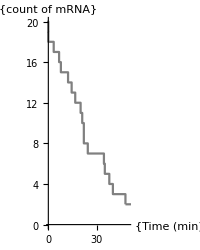

-Graphics-

### Data input *Drag and drop excel sheet into a variable named “data” below...

```mathematica
data =  {{{"","","","","","","","","",""},{"","","","","",1.1666666666666667,"<- min per frame","","",""},{"","","","","*60 means spot never disappeared","","","","",""},{"date","cell","trackN","frame B appears","frame G disappears","time B appears","time G disappears","","",""},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],6.,1.,0.,999.,0.,1165.5,"","",""},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],7.,1.,0.,999.,0.,1165.5,"","",""},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],"TL09",1.,0.,999.,0.,1165.5,"","",""},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],"TL09",11.,0.,999.,0.,1165.5,"","",""},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],"TL10",1.,0.,999.,0.,1165.5,"","",""},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL03",1.,0.,999.,0.,1665.,"*ends early ",38.333333333333336,"m post video starting"},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL03",13.,0.,12.,0.,20.,"*ends early ",38.333333333333336,"m post video starting"},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL03",23.,0.,999.,0.,1665.,"*ends early ",38.333333333333336,"m post video starting"},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL03",33.,0.,999.,0.,1665.,"*ends early ",38.333333333333336,"m post video starting"},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL03",56.,0.,999.,0.,1665.,"*ends early ",38.333333333333336,"m post video starting"},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL03",71.,0.,999.,0.,1665.,"*ends early ",38.333333333333336,"m post video starting"},{DateObject[{2019,6,23,0,0,0.},"Instant","Gregorian",-6.],"TL01",1.,9.,999.,15.,1665.,"","",""},{DateObject[{2019,6,23,0,0,0.},"Instant","Gregorian",-6.],"TL01",2.,0.,999.,0.,1665.,"","",""},{DateObject[{2018,7,15,0,0,0.},"Instant","Gregorian",-6.],"TL10",1.,0.,999.,0.,1665.,"","",""},{DateObject[{2019,9,7,0,0,0.},"Instant","Gregorian",-6.],"TL02_1",1.,0.,999.,0.,1665.,"","",""},{DateObject[{2019,9,7,0,0,0.},"Instant","Gregorian",-6.],"TL02_1",13.,0.,999.,0.,1665.,"*ends at frame 34",39.66666666666667,"m post video starting"},{DateObject[{2019,9,7,0,0,0.},"Instant","Gregorian",-6.],"TL02_1",24.,0.,999.,0.,1665.,"*ends at frame 31",36.16666666666667,"m post video starting"},{DateObject[{2019,9,7,0,0,0.},"Instant","Gregorian",-6.],"TL04_2_1",1.,0.,43.,0.,71.66666666666667,"","",""},{DateObject[{2019,9,7,0,0,0.},"Instant","Gregorian",-6.],"TL04_2_1",11.,0.,999.,0.,1665.,"","",""},{DateObject[{2019,9,7,0,0,0.},"Instant","Gregorian",-6.],"TL04_2_1",23.,0.,999.,0.,1665.,"","",""},{DateObject[{2019,9,7,0,0,0.},"Instant","Gregorian",-6.],"TL06_1",1.,0.,999.,0.,1665.,"*ends at frame 28",32.66666666666667,"m post video starting"}},{{"","","","","","",""},{"",1.1666666666666667,"<- min per frame","","frame","Min","#spots"},{"","*NOTE: A huge time means spot never disappeared","","",0.,0.,19.},{"time B appears","time G disappears","G aligned to B","",1.,0.8571428571428571,19.},{0.,1165.5,1165.5,"",2.,1.7142857142857142,19.},{0.,1165.5,1165.5,"",3.,2.571428571428571,19.},{0.,1165.5,1165.5,"",4.,3.4285714285714284,19.},{0.,1165.5,1165.5,"",5.,4.285714285714286,19.},{0.,1165.5,1165.5,"",6.,5.142857142857142,19.},{0.,1165.5,1165.5,"",7.,6.,19.},{0.,14.,14.,"",8.,6.857142857142857,19.},{0.,1165.5,1165.5,"",9.,7.7142857142857135,19.},{0.,1165.5,1165.5,"",10.,8.571428571428571,19.},{0.,1165.5,1165.5,"",11.,9.428571428571429,19.},{0.,1165.5,1165.5,"",12.,10.285714285714285,19.},{10.5,1165.5,1155.,"",13.,11.142857142857142,19.},{0.,1165.5,1165.5,"",14.,12.,18.},{0.,1165.5,1165.5,"",15.,12.857142857142856,18.},{0.,1165.5,1165.5,"",16.,13.714285714285714,18.},{0.,50.16666666666667,50.16666666666667,"",17.,14.571428571428571,18.},{0.,1165.5,1165.5,"",18.,15.428571428571427,18.},{0.,1165.5,1165.5,"",19.,16.285714285714285,18.},{0.,1165.5,1165.5,"",20.,17.142857142857142,18.},{0.,0.,0.,"",21.,18.,18.},{"","","","",22.,18.857142857142858,18.},{"","","","",23.,19.71428571428571,18.},{"","","","",24.,20.57142857142857,18.},{"","","","",25.,21.428571428571427,18.},{"","","","",26.,22.285714285714285,18.},{"","","","",27.,23.142857142857142,18.},{"","","","",28.,24.,18.},{"","","","",29.,24.857142857142854,18.},{"","","","",30.,25.71428571428571,18.},{"","","","",31.,26.57142857142857,18.},{"","","","",32.,27.428571428571427,18.},{"","","","",33.,28.285714285714285,18.},{"","","","",34.,29.142857142857142,18.},{"","","","",35.,29.999999999999996,18.},{"","","","",36.,30.857142857142854,18.},{"","","","",37.,31.71428571428571,18.},{"","","","",38.,32.57142857142857,18.},{"","","","",39.,33.42857142857142,18.},{"","","","",40.,34.285714285714285,18.},{"","","","",41.,35.14285714285714,18.},{"","","","",42.,36.,18.},{"","","","",43.,36.857142857142854,18.},{"","","","",44.,37.714285714285715,18.},{"","","","",45.,38.57142857142857,18.},{"","","","",46.,39.42857142857142,18.},{"","","","",47.,40.285714285714285,18.},{"","","","",48.,41.14285714285714,18.},{"","","","",49.,42.,18.},{"","","","",50.,42.857142857142854,18.},{"","","","",51.,43.71428571428571,17.},{"","","","",52.,44.57142857142857,17.},{"","","","",53.,45.42857142857142,17.},{"","","","",54.,46.285714285714285,17.},{"","","","",55.,47.14285714285714,17.},{"","","","",56.,48.,17.},{"","","","",57.,48.857142857142854,17.},{"","","","",58.,49.71428571428571,17.},{"","","","",59.,50.57142857142857,17.},{"","","","",60.,51.42857142857142,17.},{"","","","",61.,52.285714285714285,17.},{"","","","",62.,53.14285714285714,17.}},{{"","","","","","","",""},{"","","","","",1.1111111111111112,"<- min per frame",""},{"","","","","*NOTE: A huge time means spot never disappeared","","",""},{"cell","trackN","frame to min conversion","frame B appears","frame G disappears","time B appears","time G disappears","Time G dis - B app "},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 1",1.1111111111111112,0.,22.,0.,24.444444444444446,24.444444444444446},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 2",1.1111111111111112,2.,17.,2.2222222222222223,18.88888888888889,16.666666666666668},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 3",1.1111111111111112,2.,6.,2.2222222222222223,6.666666666666667,4.444444444444445},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 12",1.1111111111111112,0.,5.,0.,5.555555555555555,5.555555555555555},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 20",1.1111111111111112,0.,999.,0.,1110.,1110.},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA06 - 9",1.1111111111111112,3.,16.,3.3333333333333335,17.77777777777778,14.444444444444445},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA06 - 50",1.1111111111111112,19.,46.,21.11111111111111,51.111111111111114,30.000000000000004},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 1",1.1111111111111112,0.,11.,0.,12.222222222222223,12.222222222222223},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 11",1.1111111111111112,7.,23.,7.777777777777779,25.555555555555557,17.77777777777778},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 21",1.1111111111111112,"","",0.,0.,0.},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 26",1.1111111111111112,0.,41.,0.,45.55555555555556,45.55555555555556},{DateObject[{2019,5,9,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 43",1.1111111111111112,15.,999.,16.666666666666668,1110.,1093.3333333333333},{DateObject[{2019,5,10,0,0,0.},"Instant","Gregorian",-6.],"TA11 - 1",1.1111111111111112,0.,36.,0.,40.,40.},{DateObject[{2019,5,10,0,0,0.},"Instant","Gregorian",-6.],"TA11 - 6",1.1111111111111112,2.,3.,2.2222222222222223,3.3333333333333335,1.1111111111111112},{DateObject[{2019,5,10,0,0,0.},"Instant","Gregorian",-6.],"TA12 - 1",1.1111111111111112,34.,47.,37.77777777777778,52.22222222222222,14.444444444444443},{DateObject[{2019,5,10,0,0,0.},"Instant","Gregorian",-6.],"TA13 - 1",1.1111111111111112,28.,53.,31.111111111111114,58.88888888888889,27.77777777777778},{DateObject[{2019,5,10,0,0,0.},"Instant","Gregorian",-6.],"TA13 - 6",1.1111111111111112,34.,45.,37.77777777777778,50.,12.222222222222221},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1","",9.,33.,0.,0.,0.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 15","",0.,25.,0.,0.,0.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA50 -1","",0.,23.,0.,0.,0.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 1","",0.,21.,0.,0.,0.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 11","",4.,28.,0.,0.,0.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 26","",0.,1.,0.,0.,0.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 37","",9.,25.,0.,0.,0.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA04 - 3","",0.,8.,0.,0.,0.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA07 - 3","",8.,22.,0.,0.,0.}},{{"","","","","","","","","","",""},{"","","","","","",1.1111111111111112,"<- min per frame","","Min","#spots"},{"","","","","","","","","",0.,26.},{"date","cell","trackN","frame to min conversion","time B appears","time G disappears","time G dis - B app ","","",1.,26.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 1",1.,1.1111111111111112,0.,22.,22.,"","fade",2.,26.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 2",2.,1.1111111111111112,2.,17.,15.,"","fade",3.,26.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 3",3.,1.1111111111111112,2.,6.,4.,"","fade",4.,24.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 12",12.,1.1111111111111112,0.,5.,5.,"","fade",5.,23.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA05 - 20",20.,1.1111111111111112,0.,999.,999.,"","n/a",6.,23.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA06 - 5",5.,1.1111111111111112,0.,15.,15.,"","fade",7.,22.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA06 - 9",9.,1.1111111111111112,3.,16.,13.,"","quickly fades",8.,22.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA06 - 38",38.,1.1111111111111112,8.,23.,15.,"","fades",9.,22.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA06 - 42",42.,1.1111111111111112,6.,999.,993.,"","n/a",10.,22.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 1",1.,1.1111111111111112,0.,11.,11.,"","fade",11.,20.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA09 -  6 ",6.,1.1111111111111112,20.,10.,-10.,"","fade",12.,20.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 11",11.,1.1111111111111112,7.,23.,16.,"","fades",13.,18.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 26",26.,1.1111111111111112,0.,41.,41.,"","fades",14.,18.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA09 - 43",43.,1.1111111111111112,15.,999.,984.,"","n/a",15.,15.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA11 - 1","",1.1111111111111112,0.,36.,36.,"","fade",16.,14.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA11 - 6","",1.1111111111111112,2.,3.,"","*Tai doesn’t like this spot… remove?? ","hard to say",17.,14.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA12 - 1","",1.1111111111111112,34.,47.,13.,"","SPLITS!! ",18.,14.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA13 - 1","",1.1111111111111112,28.,999.,971.,"","n/a",19.,14.},{DateObject[{2019,5,8,0,0,0.},"Instant","Gregorian",-6.],"TA13 - 6","",1.1111111111111112,34.,45.,11.,"","fade",20.,14.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",1.,0.6269592476489028,15.,55.,40.,"","fade",21.,14.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 15",15.,0.6269592476489028,0.,41.666666666666664,41.666666666666664,"","hard to say",22.,13.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 28",28.,0.6269592476489028,0.,4.,4.,"","hard to say",23.,13.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA50 -1",1.,0.6269592476489028,0.,38.333333333333336,38.333333333333336,"","SPLITS!! ",24.,12.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 1",1.,0.6,0.,35.,35.,"","fade",25.,12.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 11",11.,0.6,6.666666666666667,46.666666666666664,40.,"","fade",26.,12.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 26","","",0.,2.,"","*Removed this spot bc its sketchy ","",27.,11.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 37",37.,0.6,15.,41.666666666666664,26.666666666666664,"","fade",28.,11.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA04 - 3",3.,0.6,0.,7.,7.,"","fade",29.,11.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA07 - 3",3.,0.6,13.333333333333334,36.666666666666664,23.33333333333333,"","fade",30.,11.},{" ","","","","","","","","",31.,11.},{"","","","","","","","","19/tot fade",32.,11.},{"","","","","","","","","2/tot splot ",33.,11.},{"","","","","","","","","tot = 27",34.,11.},{"","","","","","","","","",35.,10.},{"","","","","","","","","",36.,9.},{"","","","","","","","","",37.,9.},{"","","","","","","","","",38.,9.},{"","","","","","","","","",39.,8.},{"","","","","","","","","",40.,6.},{"","","","","","","","","",41.,5.},{"","","","","","","","","",42.,4.},{"","","","","","","","","",43.,4.},{"","","","","","","","","",44.,4.},{"","","","","","","","","",45.,4.},{"","","","","","","","","",46.,4.},{"","","","","","","","","",47.,4.},{"","","","","","","","","",48.,4.},{"","","","","","","","","",49.,4.},{"","","","","","","","","",50.,4.},{"","","","","","","","","",51.,4.},{"","","","","","","","","",52.,4.},{"","","","","","","","","",53.,4.},{"","","","","","","","","",54.,4.},{"","","","","","","","","",55.,4.},{"","","","","","","","","",56.,4.},{"","","","","","","","","",57.,4.},{"","","","","","","","","",58.,4.},{"","","","","","","","","",59.,4.},{"","","","","","","","","",60.,4.},{"","","","","","","","","",61.,4.},{"","","","","","","","","",62.,4.},{"","","","","","","","","",63.,4.}},{{"","","","","","","","",""},{"","","","",1.1111111111111112,"<- min per frame","frame","Min","#spots"},{"","","","","","",0.,0.,13.},{"date","cell","time B appears","time G disappears","time G dis - B app ","",1.,1.,13.},{"","","","","","",2.,2.,13.},{5.,2.,2.,17.,15.,"",3.,3.,13.},{5.,3.,2.,6.,4.,"",4.,4.,12.},{"","","","","","",5.,5.,12.},{"","","","","","",6.,6.,12.},{6.,9.,3.,16.,13.,"",7.,7.,12.},{6.,50.,19.,46.,27.,"",8.,8.,12.},{"","","","","","",9.,9.,12.},{9.,11.,7.,23.,16.,"",10.,10.,12.},{"","","","","","",11.,11.,11.},{"","","","","","",12.,12.,11.},{9.,43.,15.,999.,984.,"",13.,13.,9.},{"","","","","","",14.,14.,9.},{"","","","","","",15.,15.,8.},{12.,1.,34.,47.,13.,"",16.,16.,7.},{13.,1.,28.,53.,25.,"",17.,17.,7.},{13.,6.,34.,45.,11.,"",18.,18.,7.},{"","","","","","",19.,19.,7.},{"","","","","","",20.,20.,7.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",15.,55.,40.,"*100s int between imgs",21.,21.,7.},{"","","","","","",22.,22.,7.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA50 -1","","","","",23.,23.,7.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 1","","","","",24.,24.,6.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 11",6.666666666666667,46.666666666666664,40.,"",25.,25.,5.},{"","","","","","",26.,26.,5.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 37",15.,41.666666666666664,26.666666666666664,"",27.,27.,3.},{"","","","","","",28.,28.,3.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA07 - 3",13.333333333333334,36.666666666666664,23.33333333333333,"",29.,29.,3.},{"","","","","","",30.,30.,3.},{"","","","","","",31.,31.,3.},{"","","","","","",32.,32.,3.},{"","","","","","",33.,33.,3.},{"","","","","","",34.,34.,3.},{"","","","","","",35.,35.,3.},{"","","","","","",36.,36.,3.},{"","","","","","",37.,37.,3.},{"","","","","","",38.,38.,3.},{"","","","","","",39.,39.,3.},{"","","","","","",40.,40.,1.},{"","","","","","",41.,41.,1.},{"","","","","","",42.,42.,1.},{"","","","","","",43.,43.,1.},{"","","","","","",44.,44.,1.},{"","","","","","",45.,45.,1.},{"","","","","","",46.,46.,1.},{"","","","","","",47.,47.,1.},{"","","","","","",48.,48.,1.},{"","","","","","",49.,49.,1.},{"","","","","","",50.,50.,1.},{"","","","","","",51.,51.,1.},{"","","","","","",52.,52.,1.},{"","","","","","",53.,53.,1.},{"","","","","","",54.,54.,1.},{"","","","","","",55.,55.,1.},{"","","","","","",56.,56.,1.},{"","","","","","",57.,57.,1.},{"","","","","","",58.,58.,1.},{"","","","","","",59.,59.,1.},{"","","","","","",60.,60.,1.}},{{"CRITERIA : ","",""},{"","\"ALL\" chart : ",""},{"","","ALL white spots per cell except… "},{"","","...disappears wtihin first couple frames"},{"","","...Is too iffy (flickering, dim, not sharp point)"},{"","","…AGO2 binds spot within last 1/4 of the movie (not enough time to find out if translation shuts down)"},{"","\"AGO2-binding\" chart : ",""},{"","","ALL white spots… "},{"","","…that have a period of time BEFORE AGO2 can be detected "},{"","","The initial AGO2 binding event is thus the frame when AGO2 can first be seen "},{"","",""},{"","",""},{"NOTE!!! ","",""},{"Time listed starts counting at tme 0!!! ","",""}}}  ;
```

```mathematica
(*data =  {{{"","","","","","",""},{"","","","","",1.1111111111111112,"<- min per frame"},{"","","","","*60 means spot never disappeared","",""},{"date","cell","trackN","frame B appears","frame G disappears","time B appears","time G disappears"},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],6.,1.,0.,999.,0.,1110.},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],7.,2.,0.,999.,0.,1110.},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],9.,1.,0.,999.,0.,1110.},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],9.,11.,0.,999.,0.,1110.},{DateObject[{2019,5,28,0,0,0.},"Instant","Gregorian",-6.],10.,1.,0.,999.,0.,1110.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL07",1.,0.,999.,0.,1665.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL07",11.,0.,12.,0.,20.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL07",23.,0.,999.,0.,1665.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL07",33.,0.,999.,0.,1665.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL07",56.,0.,999.,0.,1665.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TL07",71.,0.,999.,0.,1665.}},{{"","","","","","",""},{"",1.1111111111111112,"<- min per frame","","frame","Min","#spots"},{"","*NOTE: A huge time means spot never disappeared","","",0.,0.,11.},{"time B appears","time G disappears","G aligned to B","",1.,0.8999999999999999,11.},{0.,1110.,1110.,"",2.,1.7999999999999998,11.},{0.,1110.,1110.,"",3.,2.6999999999999997,11.},{0.,1110.,1110.,"",4.,3.5999999999999996,11.},{0.,1110.,1110.,"",5.,4.5,11.},{0.,1110.,1110.,"",6.,5.3999999999999995,11.},{0.,1665.,1665.,"",7.,6.3,11.},{0.,20.,20.,"",8.,7.199999999999999,11.},{0.,1665.,1665.,"",9.,8.1,11.},{0.,1665.,1665.,"",10.,9.,11.},{0.,1665.,1665.,"",11.,9.9,11.},{0.,1665.,1665.,"",12.,10.799999999999999,11.},{"","","","",13.,11.7,11.},{"","","","",14.,12.6,11.},{"","","","",15.,13.5,11.},{"","","","",16.,14.399999999999999,11.},{"","","","",17.,15.299999999999999,11.},{"","","","",18.,16.2,11.},{"","","","",19.,17.099999999999998,11.},{"","","","",20.,18.,10.},{"","","","",21.,18.9,10.},{"","","","",22.,19.8,10.},{"","","","",23.,20.7,10.},{"","","","",24.,21.599999999999998,10.},{"","","","",25.,22.5,10.},{"","","","",26.,23.4,10.},{"","","","",27.,24.299999999999997,10.},{"","","","",28.,25.2,10.},{"","","","",29.,26.099999999999998,10.},{"","","","",30.,27.,10.},{"","","","",31.,27.9,10.},{"","","","",32.,28.799999999999997,10.},{"","","","",33.,29.7,10.},{"","","","",34.,30.599999999999998,10.},{"","","","",35.,31.5,10.},{"","","","",36.,32.4,10.},{"","","","",37.,33.3,10.},{"","","","",38.,34.199999999999996,10.},{"","","","",39.,35.1,10.},{"","","","",40.,36.,10.},{"","","","",41.,36.9,10.},{"","","","",42.,37.8,10.},{"","","","",43.,38.699999999999996,10.},{"","","","",44.,39.6,10.},{"","","","",45.,40.5,10.},{"","","","",46.,41.4,10.},{"","","","",47.,42.3,10.},{"","","","",48.,43.199999999999996,10.},{"","","","",49.,44.1,10.},{"","","","",50.,45.,10.},{"","","","",51.,45.9,10.},{"","","","",52.,46.8,10.},{"","","","",53.,47.699999999999996,10.},{"","","","",54.,48.599999999999994,10.},{"","","","",55.,49.5,10.},{"","","","",56.,50.4,10.},{"","","","",57.,51.3,10.},{"","","","",58.,52.199999999999996,10.},{"","","","",59.,53.099999999999994,10.},{"","","","",60.,54.,10.},{"","","","",61.,54.9,10.},{"","","","",62.,55.8,10.}},{{"","","","","","",""},{"","","","",1.1111111111111112,"<- min per frame",""},{"","","","*NOTE: A huge time means spot never disappeared","","",""},{"cell","trackN","frame B appears","frame G disappears","time B appears","time G disappears","Time G dis - B app "},{5.,1.,0.,22.,0.,24.444444444444446,24.444444444444446},{5.,2.,2.,17.,2.2222222222222223,18.88888888888889,16.666666666666668},{5.,3.,2.,6.,2.2222222222222223,6.666666666666667,4.444444444444445},{5.,12.,0.,5.,0.,5.555555555555555,5.555555555555555},{5.,20.,0.,999.,0.,1110.,1110.},{6.,9.,3.,16.,3.3333333333333335,17.77777777777778,14.444444444444445},{6.,50.,19.,46.,21.11111111111111,51.111111111111114,30.000000000000004},{9.,1.,0.,11.,0.,12.222222222222223,12.222222222222223},{9.,11.,7.,23.,7.777777777777779,25.555555555555557,17.77777777777778},{9.,21.,"","",0.,0.,0.},{9.,26.,0.,41.,0.,45.55555555555556,45.55555555555556},{9.,43.,15.,999.,16.666666666666668,1110.,1093.3333333333333},{11.,1.,0.,36.,0.,40.,40.},{11.,6.,2.,3.,2.2222222222222223,3.3333333333333335,1.1111111111111112},{12.,1.,34.,47.,37.77777777777778,52.22222222222222,14.444444444444443},{13.,1.,28.,53.,31.111111111111114,58.88888888888889,27.77777777777778},{13.,6.,34.,45.,37.77777777777778,50.,12.222222222222221},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",9.,33.,15.,55.,40.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 15",0.,25.,0.,41.666666666666664,41.666666666666664},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA50 -1",0.,23.,0.,38.333333333333336,38.333333333333336},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 1",0.,21.,0.,35.,35.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 11",4.,28.,6.666666666666667,46.666666666666664,40.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 26",0.,1.,0.,2.,2.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 37",9.,25.,15.,41.666666666666664,26.666666666666664},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA04 - 3",0.,8.,0.,7.,7.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA07 - 3",8.,22.,13.333333333333334,36.666666666666664,23.33333333333333}},{{"","","","","","","","",""},{"","","","",1.1111111111111112,"<- min per frame","frame","Min","#spots"},{"","","","","","",0.,0.,25.},{"date","cell","time B appears","time G disappears","time G dis - B app ","",1.,0.8999999999999999,24.},{5.,1.,0.,22.,22.,"",2.,1.7999999999999998,23.},{5.,2.,2.,17.,15.,"",3.,2.6999999999999997,23.},{5.,3.,2.,6.,4.,"",4.,3.5999999999999996,22.},{5.,12.,0.,5.,5.,"",5.,4.5,21.},{5.,20.,0.,999.,999.,"",6.,5.3999999999999995,21.},{6.,9.,3.,16.,13.,"",7.,6.3,20.},{6.,50.,19.,46.,27.,"",8.,7.199999999999999,20.},{9.,1.,0.,11.,11.,"",9.,8.1,20.},{9.,11.,7.,23.,16.,"",10.,9.,20.},{9.,21.,"","","","",11.,9.9,18.},{9.,26.,0.,41.,41.,"",12.,10.799999999999999,18.},{9.,43.,15.,999.,984.,"",13.,11.7,16.},{11.,1.,0.,36.,36.,"",14.,12.6,16.},{11.,6.,2.,3.,1.,"",15.,13.5,15.},{12.,1.,34.,47.,13.,"",16.,14.399999999999999,14.},{13.,1.,28.,53.,25.,"",17.,15.299999999999999,14.},{13.,6.,34.,45.,11.,"",18.,16.2,14.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",15.,55.,40.,"",19.,17.099999999999998,14.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 15",0.,41.666666666666664,41.666666666666664,"",20.,18.,14.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA50 -1",0.,38.333333333333336,38.333333333333336,"",21.,18.9,14.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 1",0.,35.,35.,"",22.,19.8,13.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 11",6.666666666666667,46.666666666666664,40.,"",23.,20.7,13.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 26",0.,2.,2.,"",24.,21.599999999999998,12.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 37",15.,41.666666666666664,26.666666666666664,"",25.,22.5,11.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA04 - 3",0.,7.,7.,"",26.,23.4,11.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA07 - 3",13.333333333333334,36.666666666666664,23.33333333333333,"",27.,24.299999999999997,9.},{" ","","","","","",28.,25.2,9.},{"","","","","","",29.,26.099999999999998,9.},{"","","","","","",30.,27.,9.},{"","","","","","",31.,27.9,9.},{"","","","","","",32.,28.799999999999997,9.},{"","","","","","",33.,29.7,9.},{"","","","","","",34.,30.599999999999998,9.},{"","","","","","",35.,31.5,8.},{"","","","","","",36.,32.4,7.},{"","","","","","",37.,33.3,7.},{"","","","","","",38.,34.199999999999996,7.},{"","","","","","",39.,35.1,6.},{"","","","","","",40.,36.,4.},{"","","","","","",41.,36.9,3.},{"","","","","","",42.,37.8,2.},{"","","","","","",43.,38.699999999999996,2.},{"","","","","","",44.,39.6,2.},{"","","","","","",45.,40.5,2.},{"","","","","","",46.,41.4,2.},{"","","","","","",47.,42.3,2.},{"","","","","","",48.,43.199999999999996,2.},{"","","","","","",49.,44.1,2.},{"","","","","","",50.,45.,2.},{"","","","","","",51.,45.9,2.},{"","","","","","",52.,46.8,2.},{"","","","","","",53.,47.699999999999996,2.},{"","","","","","",54.,48.599999999999994,2.},{"","","","","","",55.,49.5,2.},{"","","","","","",56.,50.4,2.},{"","","","","","",57.,51.3,2.},{"","","","","","",58.,52.199999999999996,2.},{"","","","","","",59.,53.099999999999994,2.},{"","","","","","",60.,54.,2.},{"","","","","","",61.,54.9,2.},{"","","","","","",62.,55.8,2.}},{{"","","","","","","","",""},{"","","","",1.1111111111111112,"<- min per frame","frame","Min","#spots"},{"","","","","","",0.,0.,13.},{"date","cell","time B appears","time G disappears","time G dis - B app ","",1.,0.8999999999999999,13.},{"","","","","","",2.,1.7999999999999998,13.},{5.,2.,2.,17.,15.,"",3.,2.6999999999999997,13.},{5.,3.,2.,6.,4.,"",4.,3.5999999999999996,12.},{"","","","","","",5.,4.5,12.},{"","","","","","",6.,5.3999999999999995,12.},{6.,9.,3.,16.,13.,"",7.,6.3,12.},{6.,50.,19.,46.,27.,"",8.,7.199999999999999,12.},{"","","","","","",9.,8.1,12.},{9.,11.,7.,23.,16.,"",10.,9.,12.},{"","","","","","",11.,9.9,11.},{"","","","","","",12.,10.799999999999999,11.},{9.,43.,15.,999.,984.,"",13.,11.7,9.},{"","","","","","",14.,12.6,9.},{"","","","","","",15.,13.5,8.},{12.,1.,34.,47.,13.,"",16.,14.399999999999999,7.},{13.,1.,28.,53.,25.,"",17.,15.299999999999999,7.},{13.,6.,34.,45.,11.,"",18.,16.2,7.},{"","","","","","",19.,17.099999999999998,7.},{"","","","","","",20.,18.,7.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",15.,55.,40.,"*100s int between imgs",21.,18.9,7.},{"","","","","","",22.,19.8,7.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA50 -1","","","","",23.,20.7,7.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 1","","","","",24.,21.599999999999998,6.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 11",6.666666666666667,46.666666666666664,40.,"",25.,22.5,5.},{"","","","","","",26.,23.4,5.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA02 - 37",15.,41.666666666666664,26.666666666666664,"",27.,24.299999999999997,3.},{"","","","","","",28.,25.2,3.},{DateObject[{2018,7,7,0,0,0.},"Instant","Gregorian",-6.],"TA07 - 3",13.333333333333334,36.666666666666664,23.33333333333333,"",29.,26.099999999999998,3.},{"","","","","","",30.,27.,3.},{"","","","","","",31.,27.9,3.},{"","","","","","",32.,28.799999999999997,3.},{"","","","","","",33.,29.7,3.},{"","","","","","",34.,30.599999999999998,3.},{"","","","","","",35.,31.5,3.},{"","","","","","",36.,32.4,3.},{"","","","","","",37.,33.3,3.},{"","","","","","",38.,34.199999999999996,3.},{"","","","","","",39.,35.1,3.},{"","","","","","",40.,36.,1.},{"","","","","","",41.,36.9,1.},{"","","","","","",42.,37.8,1.},{"","","","","","",43.,38.699999999999996,1.},{"","","","","","",44.,39.6,1.},{"","","","","","",45.,40.5,1.},{"","","","","","",46.,41.4,1.},{"","","","","","",47.,42.3,1.},{"","","","","","",48.,43.199999999999996,1.},{"","","","","","",49.,44.1,1.},{"","","","","","",50.,45.,1.},{"","","","","","",51.,45.9,1.},{"","","","","","",52.,46.8,1.},{"","","","","","",53.,47.699999999999996,1.},{"","","","","","",54.,48.599999999999994,1.},{"","","","","","",55.,49.5,1.},{"","","","","","",56.,50.4,1.},{"","","","","","",57.,51.3,1.},{"","","","","","",58.,52.199999999999996,1.},{"","","","","","",59.,53.099999999999994,1.},{"","","","","","",60.,54.,1.},{"","","","","","",61.,54.9,1.},{"","","","","","",62.,55.8,1.}}}   ;
```

```mathematica
(*data = {{{"","","","","",""},{"","","","",1.1111111111111112,"<- min per frame"},{"","","","*60 means spot never disappeared","",""},{"cell","trackN","frame B appears","frame G disappears","time B appears","time G disappears"},{6.,1.,0.,999.,0.,1110.},{7.,2.,0.,999.,0.,1110.},{9.,3.,0.,999.,0.,1110.},{9.,12.,0.,999.,0.,1110.},{10.,20.,0.,999.,0.,1110.},{"bc793 presentation cell","*fix w exact numbers!! ","","",0.,1110.},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""}},{{"","","","","","",""},{"",1.1111111111111112,"<- min per frame","","frame","Min","#spots"},{"","","","",0.,0.,6.},{"time B appears","time G disappears","G aligned to B","",1.,0.8999999999999999,6.},{0.,1110.,1110.,"",2.,1.7999999999999998,6.},{0.,1110.,1110.,"",3.,2.6999999999999997,6.},{0.,1110.,1110.,"",4.,3.5999999999999996,6.},{0.,1110.,1110.,"",5.,4.5,6.},{0.,1110.,1110.,"",6.,5.3999999999999995,6.},{0.,1110.,1110.,"",7.,6.3,6.},{"","","","",8.,7.199999999999999,6.},{"","","","",9.,8.1,6.},{"","","","",10.,9.,6.},{"","","","",11.,9.9,6.},{"","","","",12.,10.799999999999999,6.},{"","","","",13.,11.7,6.},{"","","","",14.,12.6,6.},{"","","","",15.,13.5,6.},{"","","","",16.,14.399999999999999,6.},{"","","","",17.,15.299999999999999,6.},{"","","","",18.,16.2,6.},{"","","","",19.,17.099999999999998,6.},{"","","","",20.,18.,6.},{"","","","",21.,18.9,6.},{"","","","",22.,19.8,6.},{"","","","",23.,20.7,6.},{"","","","",24.,21.599999999999998,6.},{"","","","",25.,22.5,6.},{"","","","",26.,23.4,6.},{"","","","",27.,24.299999999999997,6.},{"","","","",28.,25.2,6.},{"","","","",29.,26.099999999999998,6.},{"","","","",30.,27.,6.},{"","","","",31.,27.9,6.},{"","","","",32.,28.799999999999997,6.},{"","","","",33.,29.7,6.},{"","","","",34.,30.599999999999998,6.},{"","","","",35.,31.5,6.},{"","","","",36.,32.4,6.},{"","","","",37.,33.3,6.},{"","","","",38.,34.199999999999996,6.},{"","","","",39.,35.1,6.},{"","","","",40.,36.,6.},{"","","","",41.,36.9,6.},{"","","","",42.,37.8,6.},{"","","","",43.,38.699999999999996,6.},{"","","","",44.,39.6,6.},{"","","","",45.,40.5,6.},{"","","","",46.,41.4,6.},{"","","","",47.,42.3,6.},{"","","","",48.,43.199999999999996,6.},{"","","","",49.,44.1,6.},{"","","","",50.,45.,6.},{"","","","",51.,45.9,6.},{"","","","",52.,46.8,6.},{"","","","",53.,47.699999999999996,6.},{"","","","",54.,48.599999999999994,6.},{"","","","",55.,49.5,6.},{"","","","",56.,50.4,6.},{"","","","",57.,51.3,6.},{"","","","",58.,52.199999999999996,6.},{"","","","",59.,53.099999999999994,6.},{"","","","",60.,54.,6.},{"","","","",61.,54.9,6.},{"","","","",62.,55.8,6.}},{{"","","","","",""},{"","","","",1.1111111111111112,"<- min per frame"},{"","","","*60 means spot never disappeared","",""},{"cell","trackN","frame B appears","frame G disappears","time B appears","time G disappears"},{5.,1.,0.,22.,0.,24.444444444444446},{5.,2.,1.,1.,1.1111111111111112,1.1111111111111112},{5.,3.,0.,6.,0.,6.666666666666667},{5.,12.,0.,7.,0.,7.777777777777779},{5.,20.,0.,60.,0.,66.66666666666667},{6.,9.,2.,17.,2.2222222222222223,18.88888888888889},{6.,50.,19.,50.,21.11111111111111,55.55555555555556},{9.,1.,0.,11.,0.,12.222222222222223},{9.,11.,5.,23.,5.555555555555555,25.555555555555557},{9.,21.,12.,46.,13.333333333333334,51.111111111111114},{9.,26.,0.,43.,0.,47.77777777777778},{9.,43.,17.,60.,18.88888888888889,66.66666666666667},{11.,1.,0.,36.,0.,40.},{11.,6.,3.,3.,3.3333333333333335,3.3333333333333335},{12.,1.,34.,47.,37.77777777777778,52.22222222222222},{13.,1.,46.,60.,51.111111111111114,66.66666666666667},{13.,6.,41.,44.,45.55555555555556,48.88888888888889},{"bc793 presentation cell","*fix w exact numbers!! ","","",5.,40.}},{{"","","","","","","","",""},{"","","",1.1111111111111112,"<- min per frame","","frame","Min","#spots"},{"","","","","","",0.,0.,19.},{"date","cell","time B appears","time G disappears","G aligned to B","",1.,0.8999999999999999,19.},{"","",0.,24.444444444444446,24.444444444444446,"",2.,1.7999999999999998,19.},{"","",1.1111111111111112,1.1111111111111112,0.,"",3.,2.6999999999999997,19.},{"","",0.,6.666666666666667,6.666666666666667,"",4.,3.5999999999999996,18.},{"","",0.,7.777777777777779,7.777777777777779,"",5.,4.5,18.},{"","",0.,999.,999.,"",6.,5.3999999999999995,18.},{"","",2.2222222222222223,18.88888888888889,16.666666666666668,"",7.,6.3,17.},{"","",21.11111111111111,55.55555555555556,34.44444444444444,"",8.,7.199999999999999,16.},{"","",0.,12.222222222222223,12.222222222222223,"",9.,8.1,16.},{"","",5.555555555555555,25.555555555555557,20.,"",10.,9.,16.},{"","",13.333333333333334,51.111111111111114,37.77777777777778,"",11.,9.9,16.},{"","",0.,47.77777777777778,47.77777777777778,"",12.,10.799999999999999,16.},{"","",18.88888888888889,999.,980.1111111111111,"",13.,11.7,15.},{"","",0.,40.,40.,"",14.,12.6,15.},{"","",3.3333333333333335,3.3333333333333335,0.,"",15.,13.5,14.},{"","",37.77777777777778,52.22222222222222,14.444444444444443,"",16.,14.399999999999999,14.},{"","",51.111111111111114,999.,947.8888888888889,"",17.,15.299999999999999,13.},{"","",45.55555555555556,48.88888888888889,3.3333333333333357,"",18.,16.2,13.},{"","",5.,40.,35.,"",19.,17.099999999999998,13.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",12.,33.,21.,"",20.,18.,12.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 15",0.,22.,22.,"",21.,18.9,11.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA50 -1",0.,22.,22.,"",22.,19.8,9.},{"","","","","","",23.,20.7,9.},{"","","","","","",24.,21.599999999999998,9.},{"","","","","","",25.,22.5,8.},{"","","","","","",26.,23.4,8.},{"","","","","","",27.,24.299999999999997,8.},{"","","","","","",28.,25.2,8.},{"","","","","","",29.,26.099999999999998,8.},{"","","","","","",30.,27.,8.},{"","","","","","",31.,27.9,8.},{"","","","","","",32.,28.799999999999997,8.},{"","","","","","",33.,29.7,8.},{"","","","","","",34.,30.599999999999998,8.},{"","","","","","",35.,31.5,6.},{"","","","","","",36.,32.4,6.},{"","","","","","",37.,33.3,6.},{"","","","","","",38.,34.199999999999996,5.},{"","","","","","",39.,35.1,5.},{"","","","","","",40.,36.,4.},{"","","","","","",41.,36.9,4.},{"","","","","","",42.,37.8,4.},{"","","","","","",43.,38.699999999999996,4.},{"","","","","","",44.,39.6,4.},{"","","","","","",45.,40.5,4.},{"","","","","","",46.,41.4,4.},{"","","","","","",47.,42.3,4.},{"","","","","","",48.,43.199999999999996,3.},{"","","","","","",49.,44.1,3.},{"","","","","","",50.,45.,3.},{"","","","","","",51.,45.9,3.},{"","","","","","",52.,46.8,3.},{"","","","","","",53.,47.699999999999996,3.},{"","","","","","",54.,48.599999999999994,3.},{"","","","","","",55.,49.5,3.},{"","","","","","",56.,50.4,3.},{"","","","","","",57.,51.3,3.},{"","","","","","",58.,52.199999999999996,3.},{"","","","","","",59.,53.099999999999994,3.},{"","","","","","",60.,54.,3.},{"","","","","","",61.,54.9,3.},{"","","","","","",62.,55.8,3.}},{{"","","","","","","","",""},{"","","",1.1111111111111112,"<- min per frame","","frame","Min","#spots"},{"","","","","","",0.,0.,9.},{"date","cell","time B appears","time G disappears","G aligned to B","",1.,0.8999999999999999,9.},{"","","","","","",2.,1.7999999999999998,9.},{"","",1.1111111111111112,1.1111111111111112,0.,"",3.,2.6999999999999997,9.},{"","","","","","",4.,3.5999999999999996,8.},{"","","","","","",5.,4.5,8.},{"","","","","","",6.,5.3999999999999995,8.},{"","",2.2222222222222223,18.88888888888889,16.666666666666668,"",7.,6.3,8.},{"","",21.11111111111111,55.55555555555556,34.44444444444444,"",8.,7.199999999999999,8.},{"","","","","","",9.,8.1,8.},{"","",5.555555555555555,25.555555555555557,20.,"",10.,9.,8.},{"","",13.333333333333334,51.111111111111114,37.77777777777778,"",11.,9.9,8.},{"","","","","","",12.,10.799999999999999,8.},{"","",18.88888888888889,999.,980.1111111111111,"",13.,11.7,8.},{"","","","","","",14.,12.6,8.},{"","","","","","",15.,13.5,7.},{"","",37.77777777777778,52.22222222222222,14.444444444444443,"",16.,14.399999999999999,7.},{"","","","","","",17.,15.299999999999999,6.},{"","",45.55555555555556,48.88888888888889,3.3333333333333357,"",18.,16.2,6.},{"","",5.,40.,35.,"",19.,17.099999999999998,6.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",12.,33.,21.,"",20.,18.,5.},{"","","","","","",21.,18.9,4.},{"","","","","","",22.,19.8,4.},{"","","","","","",23.,20.7,4.},{"","","","","","",24.,21.599999999999998,4.},{"","","","","","",25.,22.5,4.},{"","","","","","",26.,23.4,4.},{"","","","","","",27.,24.299999999999997,4.},{"","","","","","",28.,25.2,4.},{"","","","","","",29.,26.099999999999998,4.},{"","","","","","",30.,27.,4.},{"","","","","","",31.,27.9,4.},{"","","","","","",32.,28.799999999999997,4.},{"","","","","","",33.,29.7,4.},{"","","","","","",34.,30.599999999999998,4.},{"","","","","","",35.,31.5,2.},{"","","","","","",36.,32.4,2.},{"","","","","","",37.,33.3,2.},{"","","","","","",38.,34.199999999999996,1.},{"","","","","","",39.,35.1,1.},{"","","","","","",40.,36.,1.},{"","","","","","",41.,36.9,1.},{"","","","","","",42.,37.8,1.},{"","","","","","",43.,38.699999999999996,1.},{"","","","","","",44.,39.6,1.},{"","","","","","",45.,40.5,1.},{"","","","","","",46.,41.4,1.},{"","","","","","",47.,42.3,1.},{"","","","","","",48.,43.199999999999996,1.},{"","","","","","",49.,44.1,1.},{"","","","","","",50.,45.,1.},{"","","","","","",51.,45.9,1.},{"","","","","","",52.,46.8,1.},{"","","","","","",53.,47.699999999999996,1.},{"","","","","","",54.,48.599999999999994,1.},{"","","","","","",55.,49.5,1.},{"","","","","","",56.,50.4,1.},{"","","","","","",57.,51.3,1.},{"","","","","","",58.,52.199999999999996,1.},{"","","","","","",59.,53.099999999999994,1.},{"","","","","","",60.,54.,1.},{"","","","","","",61.,54.9,1.},{"","","","","","",62.,55.8,1.}}};
```

```mathematica
data [[1]]//TableForm
```

|  |  |  |  |  |  |  |  | 
 |  |  |  |  | 1.16667 | <- min per frame |  |  | 
 |  |  |  | *60 means spot never disappeared |  |  |  |  | 
date | cell | trackN | frame B appears | frame G disappears | time B appears | time G disappears |  |  | 
Tue 28 May 2019 00:00:00GMT-6. | 6. | 1. | 0. | 999. | 0. | 1165.5 |  |  | 
Tue 28 May 2019 00:00:00GMT-6. | 7. | 1. | 0. | 999. | 0. | 1165.5 |  |  | 
Tue 28 May 2019 00:00:00GMT-6. | TL09 | 1. | 0. | 999. | 0. | 1165.5 |  |  | 
Tue 28 May 2019 00:00:00GMT-6. | TL09 | 11. | 0. | 999. | 0. | 1165.5 |  |  | 
Tue 28 May 2019 00:00:00GMT-6. | TL10 | 1. | 0. | 999. | 0. | 1165.5 |  |  | 
Sat 7 Jul 2018 00:00:00GMT-6. | TL03 | 1. | 0. | 999. | 0. | 1665. | *ends early  | 38.3333 | m post video starting
Sat 7 Jul 2018 00:00:00GMT-6. | TL03 | 13. | 0. | 12. | 0. | 20. | *ends early  | 38.3333 | m post video starting
Sat 7 Jul 2018 00:00:00GMT-6. | TL03 | 23. | 0. | 999. | 0. | 1665. | *ends early  | 38.3333 | m post video starting
Sat 7 Jul 2018 00:00:00GMT-6. | TL03 | 33. | 0. | 999. | 0. | 1665. | *ends early  | 38.3333 | m post video starting
Sat 7 Jul 2018 00:00:00GMT-6. | TL03 | 56. | 0. | 999. | 0. | 1665. | *ends early  | 38.3333 | m post video starting
Sat 7 Jul 2018 00:00:00GMT-6. | TL03 | 71. | 0. | 999. | 0. | 1665. | *ends early  | 38.3333 | m post video starting
Sun 23 Jun 2019 00:00:00GMT-6. | TL01 | 1. | 9. | 999. | 15. | 1665. |  |  | 
Sun 23 Jun 2019 00:00:00GMT-6. | TL01 | 2. | 0. | 999. | 0. | 1665. |  |  | 
Sun 15 Jul 2018 00:00:00GMT-6. | TL10 | 1. | 0. | 999. | 0. | 1665. |  |  | 
Sat 7 Sep 2019 00:00:00GMT-6. | TL02_1 | 1. | 0. | 999. | 0. | 1665. |  |  | 
Sat 7 Sep 2019 00:00:00GMT-6. | TL02_1 | 13. | 0. | 999. | 0. | 1665. | *ends at frame 34 | 39.6667 | m post video starting
Sat 7 Sep 2019 00:00:00GMT-6. | TL02_1 | 24. | 0. | 999. | 0. | 1665. | *ends at frame 31 | 36.1667 | m post video starting
Sat 7 Sep 2019 00:00:00GMT-6. | TL04_2_1 | 1. | 0. | 43. | 0. | 71.6667 |  |  | 
Sat 7 Sep 2019 00:00:00GMT-6. | TL04_2_1 | 11. | 0. | 999. | 0. | 1665. |  |  | 
Sat 7 Sep 2019 00:00:00GMT-6. | TL04_2_1 | 23. | 0. | 999. | 0. | 1665. |  |  | 
Sat 7 Sep 2019 00:00:00GMT-6. | TL06_1 | 1. | 0. | 999. | 0. | 1665. | *ends at frame 28 | 32.6667 | m post video starting

### Creating Survival Plots

#### Options/data

OPTIONS of survival plots :

```mathematica
color1 = RGBColor[0.12, 0.77, 0.61] ;
color2 = RGBColor[0.66, 0.06, 0.78] ;
color3 = RGBColor[0.9500000000000001, Rational[2, 3], 0] ;
```

```mathematica
survivalPlotOptions = {   AspectRatio->1 , LabelStyle->{ FontFamily->"Arial Narrow",32,GrayLevel[.2]} ,  PlotStyle->Black};
```

NOTE! You’ll have to manually change the 5;;25 to fit ALL your data.

```mathematica
dataTL = data[[1,5;;25 , 5;;7]] 
Length@dataTL
```

{{999.,0.,1165.5},{999.,0.,1165.5},{999.,0.,1165.5},{999.,0.,1165.5},{999.,0.,1165.5},{999.,0.,1665.},{12.,0.,20.},{999.,0.,1665.},{999.,0.,1665.},{999.,0.,1665.},{999.,0.,1665.},{999.,15.,1665.},{999.,0.,1665.},{999.,0.,1665.},{999.,0.,1665.},{999.,0.,1665.},{999.,0.,1665.},{43.,0.,71.6667},{999.,0.,1665.},{999.,0.,1665.},{999.,0.,1665.}}

21

```mathematica
data[[4,5;;33,5;;7]]
```

{{0.,22.,22.},{2.,17.,15.},{2.,6.,4.},{0.,5.,5.},{0.,999.,999.},{0.,15.,15.},{3.,16.,13.},{8.,23.,15.},{6.,999.,993.},{0.,11.,11.},{20.,10.,-10.},{7.,23.,16.},{0.,41.,41.},{15.,999.,984.},{0.,36.,36.},{2.,3.,},{34.,47.,13.},{28.,999.,971.},{34.,45.,11.},{15.,55.,40.},{0.,41.6667,41.6667},{0.,4.,4.},{0.,38.3333,38.3333},{0.,35.,35.},{6.66667,46.6667,40.},{0.,2.,},{15.,41.6667,26.6667},{0.,7.,7.},{13.3333,36.6667,23.3333}}

```mathematica
dataTA = data[[4,5;;33, 5;;7]] 
Length@dataTA
```

{{0.,22.,22.},{2.,17.,15.},{2.,6.,4.},{0.,5.,5.},{0.,999.,999.},{0.,15.,15.},{3.,16.,13.},{8.,23.,15.},{6.,999.,993.},{0.,11.,11.},{20.,10.,-10.},{7.,23.,16.},{0.,41.,41.},{15.,999.,984.},{0.,36.,36.},{2.,3.,},{34.,47.,13.},{28.,999.,971.},{34.,45.,11.},{15.,55.,40.},{0.,41.6667,41.6667},{0.,4.,4.},{0.,38.3333,38.3333},{0.,35.,35.},{6.66667,46.6667,40.},{0.,2.,},{15.,41.6667,26.6667},{0.,7.,7.},{13.3333,36.6667,23.3333}}

29

```mathematica
cutoff = 50 ;  (* I don't want to include data that Y -> W really late, so ~50 is my cutoff for detecting binding events. Any binding events after 50 will not be counted because they will look like a forever white spot... *)
dataTAbinding = Select [ dataTA, #[[1]]>0  &&  #[[1]] <cutoff & ]  ;
dataTAbinding//Length
```

16

#### TA : Survival plot of all white spots with AGO binding detection :

COUNT :

{{993.,1},{984.,2},{971.,3},{40.,4},{40.,5},{26.6667,6},{23.3333,7},{16.,8},{15.,9},{15.,10},{13.,11},{13.,12},{11.,13},{4.,14}}

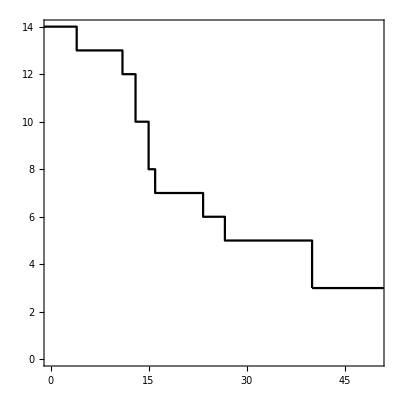

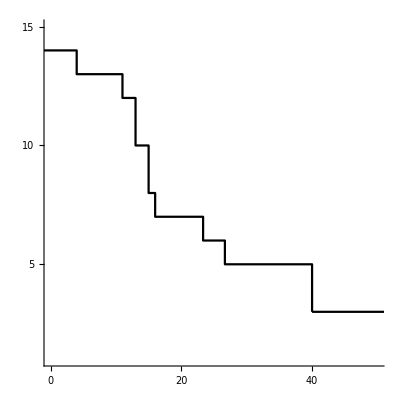

```mathematica
a = Select[ dataTAbinding[[All,3]] , #>0&]//Sort[#,Greater]&  ;
dataTAbinding0 = a ;
b = Range[1,Length@dataTAbinding0] ; 
survivalPlotData = Transpose[{a,b}]
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , (* detailed plot theme is Fing up the range and ticks...  *) Ticks-> {Range[0,50,20],Range[0,15,5] }  , survivalPlotOptions[[All]] , PlotTheme->"Detailed"   ]
ListStepPlot[ survivalPlotData,  PlotRange->{{0,50},{All,15}},Ticks-> {Range[0,50,20],Range[0,15,5] }    ,survivalPlotOptions[[All]]   ]
```

```mathematica
(*Range of axis #s... Make more or less to get rid of crowding *){Range[0,50,5],Range[0,10,5] }
```

{{0,5,10,15,20,25,30,35,40,45,50},{0,5,10}}

```mathematica
survivalPlotData = Transpose[{a,b}]
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]] ,PlotTheme->"Detailed" , Ticks-> {Range[0,50,20],Range[0,15,5] }  ]
```

{{993.,1},{984.,2},{971.,3},{40.,4},{40.,5},{26.6667,6},{23.3333,7},{16.,8},{15.,9},{15.,10},{13.,11},{13.,12},{11.,13},{4.,14}}

-Graphics-

PERCENTAGE :

{993.,984.,971.,40.,40.,26.6667,23.3333,16.,15.,15.,13.,13.,11.,4.}

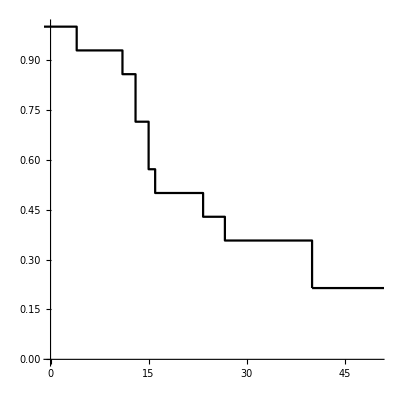

```mathematica
a = Select[ dataTAbinding[[All,3]], #>0&]//Sort[#,Greater]& 
b = Range[1,Length@a]  / Length@a; 
survivalPlotData = Transpose[{a,b}];
survivalPlotTA =ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

#### TA : Survival plot of all white spots :

```mathematica
(*Use previously determined cutoff to remove any spots that become white too late (after frame 'cutoff' *)
dataTAall = Select [ dataTA,    #[[1]] <cutoff & ] ;
dataTAall//Length
```

29

COUNT :

{999.,993.,984.,971.,41.6667,41.,40.,40.,38.3333,36.,35.,26.6667,23.3333,22.,16.,15.,15.,15.,13.,13.,11.,11.,7.,5.,4.,4.,0}

{{999.,1},{993.,2},{984.,3},{971.,4},{41.6667,5},{41.,6},{40.,7},{40.,8},{38.3333,9},{36.,10},{35.,11},{26.6667,12},{23.3333,13},{22.,14},{16.,15},{15.,16},{15.,17},{15.,18},{13.,19},{13.,20},{11.,21},{11.,22},{7.,23},{5.,24},{4.,25},{4.,26},{0,27}}

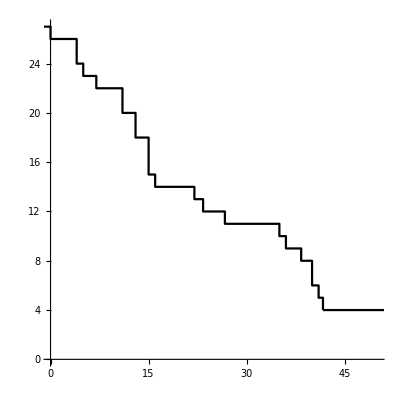

```mathematica
a = Select[ dataTAall[[All,3]], #>0&]//Sort[#,Greater]&  //Flatten[{#,0}]& (*The flatten 0 makes the line connect to the Yaxis*)
dataTAall0 = a;
b = Range[1,Length@a] ; 
survivalPlotData = Transpose[{a,b}]
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

PERCENTAGE :

```mathematica
countTA = Length@a
```

27

```mathematica
Length@a
Length@b0
```

27

0

{{999.,0.037037},{993.,0.0740741},{984.,0.111111},{971.,0.148148},{41.6667,0.185185},{41.,0.222222},{40.,0.259259},{40.,0.296296},{38.3333,0.333333},{36.,0.37037},{35.,0.407407},{26.6667,0.444444},{23.3333,0.481481},{22.,0.518519},{16.,0.555556},{15.,0.592593},{15.,0.62963},{15.,0.666667},{13.,0.703704},{13.,0.740741},{11.,0.777778},{11.,0.814815},{7.,0.851852},{5.,0.888889},{4.,0.925926},{4.,0.962963},{0.,1.}}

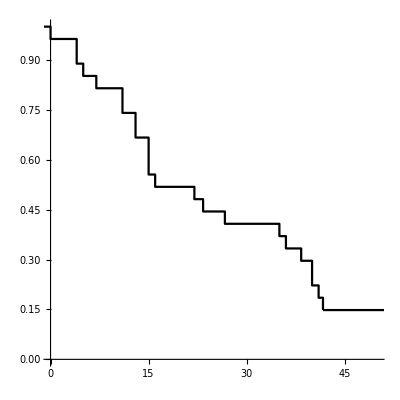

```mathematica
a = Select[ dataTAall[[All,3]], #>0&]//Sort[#,Greater]&  //Flatten[{#,0}]& (*The flatten 0 makes the line connect to the Yaxis*) ;

b = Range[1,Length@a]/(Length@a )  ;
(*a = Join[a0, {0} ]  
b = Join[Range[1,Length@b0 ]  , {Length@b0 }]  *)

survivalPlotData = Transpose[{a,b}]//N
survivalPlotDataTA = survivalPlotData;
survivalPlotTAall = ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

#### TL : Survival plot of all white spots :

NOTE! I had to add a funky extra # because the plot was a plateau and was messing up ...

```mathematica
(*Not using a 'cutoff' , I know all the spots are OK *)
dataTL0 = dataTL[[All,1]] //Sort[#,Greater]&  (*//#-1108 &  *)
```

{999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,43.,12.}

COUNT :

```mathematica
{Length@dataTL0}
 {Length@dataTA}
```

{21}

{29}

```mathematica
Join[Range[1,Length@a ]  , {Length@a }]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,27}

```mathematica
a = Join[dataTL0, {0} ]  
b =  Range[1,Length@a ]  
Length/@{a,b}
```

{999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,43.,12.,0}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

{22,22}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

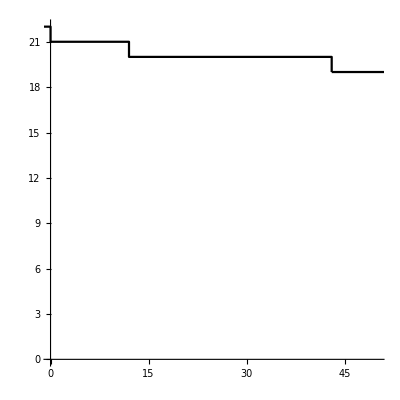

```mathematica
a = Join[dataTL0, {0} ] ;
b =  Range[1,Length@a ]  
survivalPlotData = Transpose[{a,b}] ;
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

PERCENTAGE :

```mathematica
countTL = Length@dataTL0
```

21

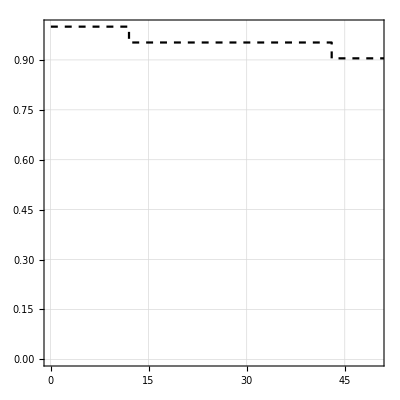

```mathematica
a = Join[dataTL0, {0} ]  ;
b = Join[Range[1,Length@dataTL0 ]  , {Length@dataTL0 }]  / countTL ;

survivalPlotData = Transpose[{a,b}]  ;
survivalPlotDataTL = survivalPlotData; 
survivalPlotTL =ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} ,PlotTheme->"Detailed" , PlotStyle-> {  Black,Dashed},survivalPlotOptions[[All]] ]
```

### Show all plots overlay

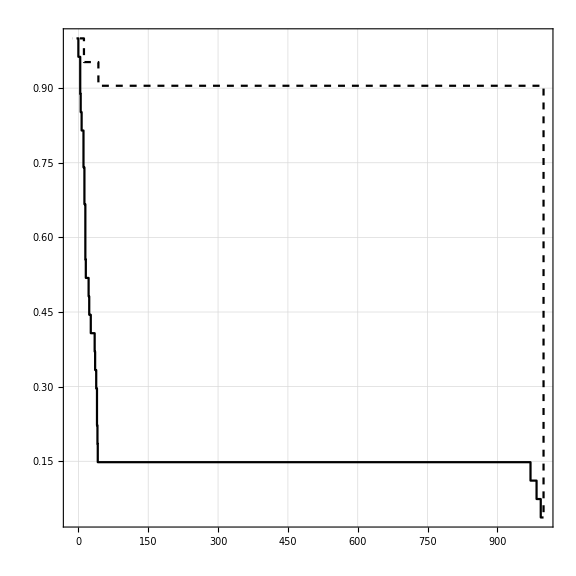

```mathematica
mySurvivalPlot = Show[ survivalPlotTL ,survivalPlotTAall, AspectRatio->1,ImageSize->Large, PlotRange->{{0,60},{0,All}}]
```

```mathematica
Export["/Volumes/BITTY/_60-90m/mySurvivalPlot.png",mySurvivalPlot]
```

/Volumes/BITTY/_60-90m/mySurvivalPlot.png

# Error Determination: bootstrapping (dev)

### BOOTSTRAPPING for error in Survival Plot :

#### Setting bootstrapping Parameters:

```mathematica
tempdata =  {dataTL0,dataTAall0};
```

```mathematica
sampleSize = Length/@tempdata  
(* sampleSize usually uses the same # as sample size, in my case, number of mRNA*) 
repetitions = 10000;  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

{21,27}

#### Setting bootstrapping Parameters:

```mathematica
(* times =  Table[ Range[1,Length@tempdata⟦i⟧] , {i,1,2}] *)
times = Table[Range[1,repetitions],2];
```

```mathematica
tempdata =  {dataTL0,dataTAall0}
```

{{999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,999.,43.,12.},{999.,993.,984.,971.,41.6667,41.,40.,40.,38.3333,36.,35.,26.6667,23.3333,22.,16.,15.,15.,15.,13.,13.,11.,11.,7.,5.,4.,4.,0}}

```mathematica
sampleSize = Length/@tempdata  
(* sampleSize usually uses the same # as sample size, in my case, number of mRNA*) 
repetitions = 100;  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

{21,27}

```mathematica
a = Table[Table[Table[RandomChoice[tempdata[[i]]],sampleSize⟦i⟧],repetitions ],{i,1,Length@tempdata,1}];
```

```mathematica
Dimensions/@a
```

{{100,21},{100,27}}

#### Bootstrapping TA :

```mathematica
Dimensions@a[[2]]
times2 = Table[ Range[1,Length@a[[2,1]]] , Length@a[[2]] ]  / Length@a[[2,1]];
Dimensions@times2
```

{100,27}

{100,27}

```mathematica
sortedAlist = Sort[#,Greater]&/@a[[2]] ;
```

```mathematica
stuff = Table[ Transpose@{sortedAlist ⟦i⟧,  times2⟦i⟧ } , {i,1,Length@a[[2]]}] ;
```

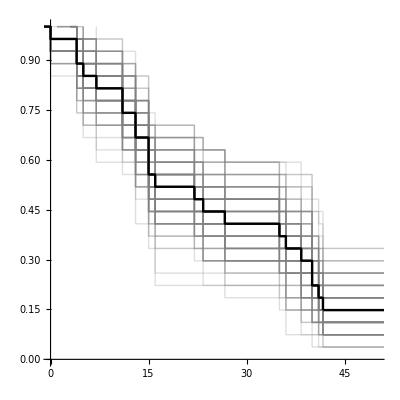

```mathematica
Show[survivalPlotTAall,  ListStepPlot[#,PlotRange->{{0,50},{All,All}}, PlotStyle->{Thin,Opacity[0.25,Gray]}]&/@stuff  ,survivalPlotTAall ]
```

#### Bootstrapping TL :

```mathematica
type = 1;
```

```mathematica
Dimensions@a[[type]]
times2 = Table[ Range[1,Length@a[[type,1]]] , Length@a[[type]] ]  / Length@a[[type,1]];
Dimensions@times2
```

{100,21}

{100,21}

```mathematica
sortedAlist = Sort[#,Greater]&/@a[[type]] ;
```

```mathematica
stuff = Table[ Transpose@{sortedAlist ⟦i⟧,  times2⟦i⟧ } , {i,1,Length@a[[type]]}] ;
```

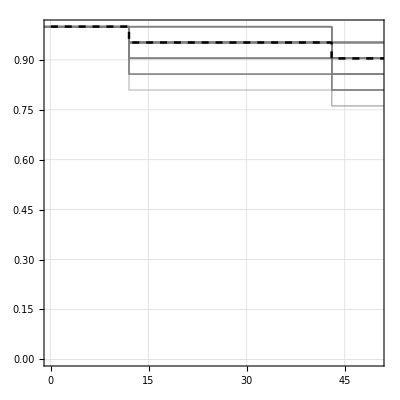

```mathematica
Show[survivalPlotTL,  ListStepPlot[#,PlotRange->{{0,50},{All,All}}, PlotStyle->{Thin,Opacity[0.25,Gray]}]&/@stuff  ,survivalPlotTL ]
```

# Error Determination: SurvivalModelFit (dev)

### SURVIVAL ERROR for error in Survival Plot :

#### Create survival model :

```mathematica
tempdata =  {dataTL0,dataTAall0};
```

```mathematica
𝒮TA=SurvivalModelFit[dataTAall0]
𝒮TL=SurvivalModelFit[dataTL0]
```

SurvivalModel[…]

SurvivalModel[…]

#### TL :

Show::gcomb: Could not combine the graphics objects in Show[,c,,GridLines→{None,Automatic},Frame→True].

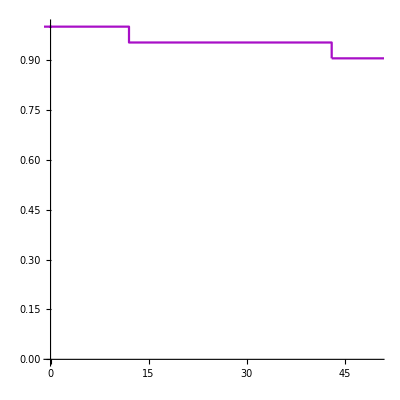
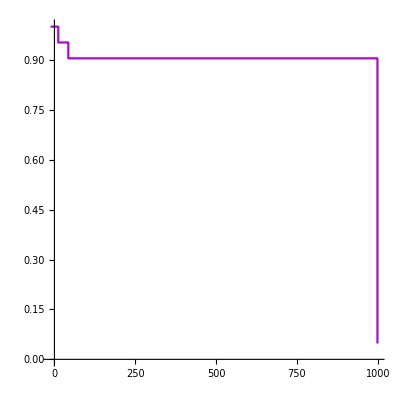
Show[-Graphics-,c,-Graphics-,GridLines→{None,Automatic},Frame→True]

```mathematica
tlErrorPlot = Show[  ListStepPlot[survivalPlotDataTL,PlotStyle->color2, PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]   ,c, ListStepPlot[survivalPlotData,PlotStyle->color2 , survivalPlotOptions[[All]]],GridLines->{None,Automatic},Frame->True]
```

```mathematica
c = Plot[{𝒮TL[x],𝒮TL["PointwiseBands"][x]},{x,0,60} ,    PlotStyle->Opacity[0,White],  Filling->{1->{{2},Opacity[.15,color2]}}];
```

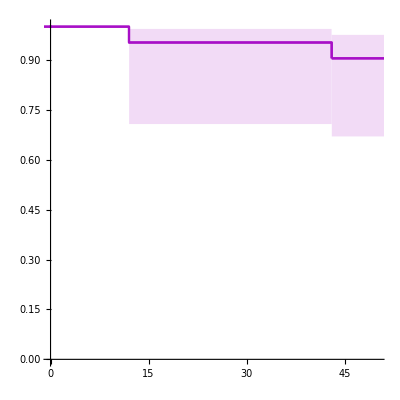

```mathematica
tlErrorPlot = Show[  ListStepPlot[survivalPlotDataTL,PlotStyle->color2, PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]   ,c, ListStepPlot[survivalPlotData,PlotStyle->color2 , survivalPlotOptions[[All]]] ]
```

#### TA :

```mathematica
c = Plot[{𝒮TA[x],𝒮TA["PointwiseBands"][x]},{x,0,60} ,    PlotStyle->Opacity[0,White],  Filling->{1->{{2},Opacity[.15,color3]}}];
```

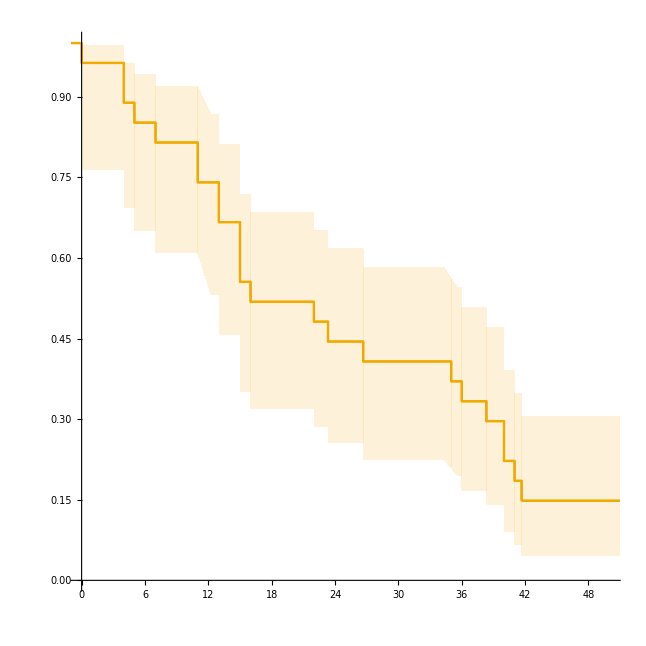

```mathematica
taErrorPlot = Show[  ListStepPlot[survivalPlotDataTA,PlotStyle-> color3, PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]   ,c, ListStepPlot[survivalPlotDataTA,PlotStyle-> color3,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]  ]
```

#### TA and TL overlay plot with 95% confidence interval error :

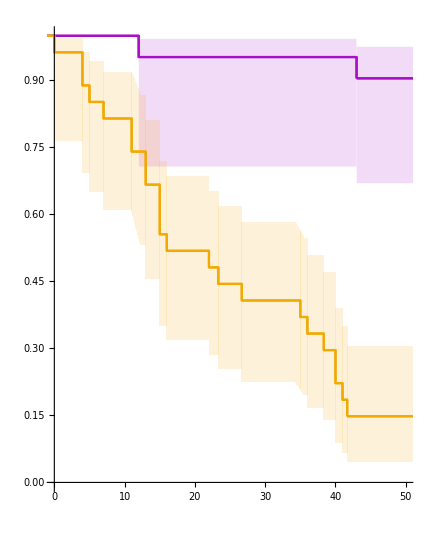

```mathematica
Show[tlErrorPlot, taErrorPlot, AspectRatio-> 1.25]
```